## Calculate Lyapunov exponent

```mathematica
(* first run long ode solver for t > 1000 and obtain a points on ther orbit of attaractor. Set those points as x0,y0,and z0 (eg. solList[[1,1]][1000]=x0)*)
xmin =.1; xmax = 5;
ymin =.1; ymax = 8;
zmin = 0; zmax = 2 π;
wmin=0;wmax=5
f[x_,y_,z_,w_]:=y;
g[x_,y_,z_,w_]:=-k1/m1 x-k2/m1(x-z);
h[x_,y_,z_,w_]:=w;
a[x_,y_,z_,w_]:=-k3/m2 z+k2/m2(x-z);
```

5

### solving 2 close orbits

```mathematica
k1=1
k2=0.5
k3=3
m1=2
m2=1
x0=1
y0=2
z0=-1
w0=0
```

2

1

3

0.1

1

1

2

-1

0

1

1

1

«3 more identical outputs»

0

-1

0

```mathematica
(* for loop for solving ODE longer*)
solList={};
tstep =100;
steps =1;
Module[{xinit, yinit, zinit,winit, xsol1, ysol1, zsol1,wsol1, tStart, tEnd, x, y, z1,w,j},
xinit = x0-.001; yinit=y0-.001; zinit=z0-.001;winit=w0-.001;
Print[zinit];
tStart =0;tEnd =tstep;
For[j = 0, j<steps, j++,
{xsol1, ysol1, zsol1,wsol1} =NDSolveValue[SetPrecision[{x'[t] == f[x[t],y[t],z1[t],w[t]],y'[t]==g[x[t],y[t],z1[t],w[t]],z1'[t]==h[x[t],y[t],z1[t],w[t]],w'[t]==a[x[t],y[t],z1[t],w[t]],x[tStart]==xinit,y[tStart]==yinit,z1[tStart]==zinit,w[tStart]==winit},1000],{x,y,z1,w},{t,tStart,tEnd},PrecisionGoal->ControlActive[4,8],WorkingPrecision->ControlActive[MachinePrecision,20]];
list = {xsol1, ysol1, zsol1,wsol1};
AppendTo[solList, list];
xinit = xsol1[tEnd];
yinit = ysol1[tEnd];
zinit = zsol1[tEnd];
winit = wsol1[tEnd];
tStart += tstep;
tEnd += tstep;
]]
solList2={};
tstep =100;
steps =1;
Module[{xinit, yinit, zinit,winit, xsol1, ysol1, zsol1,wsol1, tStart, tEnd, x, y, z1,w,j},
xinit = x0; yinit=y0; zinit=z0;winit=w0;tStart =0;tEnd =tstep;
For[j = 0, j<steps, j++,
{xsol1, ysol1, zsol1,wsol1} =NDSolveValue[SetPrecision[{x'[t] == f[x[t],y[t],z1[t],w[t]],y'[t]==g[x[t],y[t],z1[t],w[t]],z1'[t]==h[x[t],y[t],z1[t],w[t]],w'[t]==a[x[t],y[t],z1[t],w[t]],x[tStart]==xinit,y[tStart]==yinit,z1[tStart]==zinit,w[tStart]==winit},1000],{x,y,z1,w},{t,tStart,tEnd},PrecisionGoal->ControlActive[4,8],WorkingPrecision->ControlActive[MachinePrecision,20]];
list = {xsol1, ysol1, zsol1,wsol1};
AppendTo[solList2, list];
xinit = xsol1[tEnd];
yinit = ysol1[tEnd];
zinit = zsol1[tEnd];
winit = wsol1[tEnd];
tStart += tstep;
tEnd += tstep;
]]
```

-1.001

### Calculating λ

```mathematica
logDelta[t_]:= Module[{deltaX, deltaY,dist,deltaZ,deltaW},
deltaX = solList[[1,1]][t]-solList2[[1,1]][t];
deltaY = solList[[1,2]][t] - solList2[[1,2]][t];
deltaZ = solList[[1,3]][t] - solList2[[1,3]][t];
deltaW = solList[[1,4]][t] - solList2[[1,4]][t];

dist = Sqrt[deltaZ^2 + deltaX^2 + deltaY^2+ deltaW^2];
Log[dist]]
```

```mathematica
(* manipulate for linear fitting *)
Manipulate[Show[Plot[logDelta[t],{t,0,100},AxesLabel->{"ω_ct","ln|δ|"},PlotLabel->"λ∼0.09"],Plot[b + a t,{t,0,50},PlotStyle->Orange]],{a,0,2},{b,1,-10}]
```

```mathematica
pts=Table[logDelta[t],{t,0,50,0.1}];
```

```mathematica
lm = LinearModelFit[pts,t,t]
```

FittedModel[-5.85224+4.13831×10^-6 t]

```mathematica
lm[20]
```

-5.85215

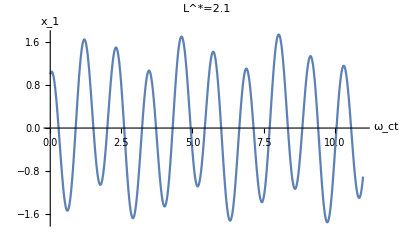

```mathematica
pieceX ={};
For[j =1, j<=Length[solList],j++,
AppendTo[pieceX, {solList[[j,1]][t],t≥100(j-1)&&t≤100 j}]]
Plot[Piecewise[pieceX],{t,0,11}, AxesLabel->{"ω_ct", "x_1"}, PlotLabel->"L^*=2.1"]
```

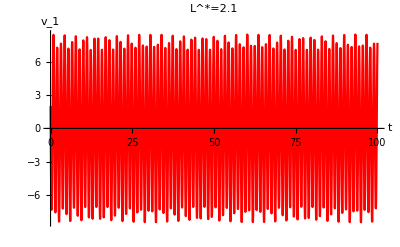

```mathematica
pieceY ={};
For[j =1, j<=Length[solList],j++,
AppendTo[pieceY, {solList[[j,2]][t],t≥100(j-1)&&t≤100 j}]]
Plot[Piecewise[pieceY],{t,0,100},PlotStyle->Red,AxesLabel->{"t", "v_1"}, PlotLabel->"L^*=2.1"]
```